```mathematica
B[r_,b_,L_,d_]:=(b/2)[(L+r)/(√((d/2)^2+(L+r)^2))-r/(√((d/2)^2+r^2))]
```

```mathematica
d:=32*10^-3 (* m *)
```

```mathematica
L:=2*10^-3 (* m *)
b:=1.3 (* T *)
Subscript[m, 2]:=0.216*10^-3 (* kg *)
```

```mathematica
D[√(q^2+(o+r)^2),r]
```

(o+r)/(√(q^2+(o+r)^2))

```mathematica
D[r/(√((d_/2)^2+r^2)),r]
```

-r^2/((r^2+d_^2/4)^(3/2))+1/(√(r^2+d_^2/4))

```mathematica
D[(L_+r)/(√((d_/2)^2+(L_+r)^2)),r]
```

-(r+L_)^2/((d_^2/4+(r+L_)^2)^(3/2))+1/(√(d_^2/4+(r+L_)^2))

```mathematica
Subscript[F, r][r_]:=-Subscript[m, 2]*b/2*D[(L+r)/(√((d/2)^2+(L+r)^2))-r/(√((d/2)^2+r^2)),r]
```

```mathematica
Subscript[F, r][r_]=-0.216*b/2*D[(L+r)/(√((d/2)^2+(L+r)^2))-r/(√((d/2)^2+r^2)),r]
```

-0.1404 (r^2/((256+r^2)^(3/2))-1/(√(256+r^2))-(1/500+r)^2/((256+(1/500+r)^2)^(3/2))+1/(√(256+(1/500+r)^2)))

```mathematica
Subscript[F, r][0.005]
```

1.23398×10^-9

```mathematica
Subscript[m, 1]:=Subscript[m, 2]
Subscript[F, rv][r_]=D[(4π*10^-7*2 Subscript[m, 1])/(4π*r^3),r]*-Subscript[m, 2]
```

(2.79936×10^-14)/r^4

```mathematica
load=(Subscript[F, rv][0.0005])/9.81
```

0.0456572

```mathematica
Assuming[α>0&&β>0&&Subscript[x, f]>0&&Subscript[x, i]>0&&ρ>0&&Δt>0&&Subscript[c, d]>0&&Subscript[A, e]>0&&Subscript[A, c]>0,
TrueQ[FullSimplify[((α*Subscript[x, f]+β)/ρ-(α*Subscript[x, i]+β)/ρ)/Δt+Subscript[c, d]*Subscript[A, e] √(2*g*(α*Subscript[x, f]+β)/(ρ*Subscript[A, c]))==α/(ρ*Δt)(Subscript[x, f]-Subscript[x, i])+Subscript[c, d]*Subscript[A, e] √(2*g*(α*Subscript[x, f]+β)/(ρ*Subscript[A, c]))]]]
```

True

```mathematica
γ:=(12*6894.76)/1000^2
```

```mathematica
Solve[B==α(((9810m)/(γ*25π*(1+2*1.25^2))+2)/(√(((9810m)/(γ*25π*(1+2*1.25^2))+2)^2+25))-((9810m)/(γ*25π*(1+2*1.25^2)))/(√(((9810m)/(γ*25π*(1+2*1.25^2)))^2+25))),m]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{m→Root[6.4339255024969×10^110 B^4-1.7748760006888×10^110 B^2 α^2+1.2240524142681×10^109 α^4+(6.4956526117474×10^112 B^4-7.3916046961263×10^112 B^2 α^2+8.9595208437894×10^111 α^4) #1+(1.4476723038019×10^115 B^4-1.8837774372235×10^115 B^2 α^2+1.6394929827881×10^114 α^4) #1^2+(9.9603001035662×10^116 B^4-2.0880629132777×10^117 B^2 α^2-1.9439518569665×10^100 α^4) #1^3+(1.1344190512709×10^119 B^4-2.5832957257357×10^119 B^2 α^2-1.2611655392279×10^102 α^4) #1^4+(5.0791490957908×10^120 B^4-1.5494619393488×10^121 B^2 α^2+6.151430406534×10^87 α^4) #1^5+(3.6471224275309×10^122 B^4-1.1647261945986×10^123 B^2 α^2+2.4253512122862×10^89 α^4) #1^6+(8.6113931566831×10^123 B^4-3.4445572626732×10^124 B^2 α^2) #1^7+(3.9394736890974×10^125 B^4-1.575789475639×10^126 B^2 α^2) #1^8&,1]},{m→Root[6.4339255024969×10^110 B^4-1.7748760006888×10^110 B^2 α^2+1.2240524142681×10^109 α^4+(6.4956526117474×10^112 B^4-7.3916046961263×10^112 B^2 α^2+8.9595208437894×10^111 α^4) #1+(1.4476723038019×10^115 B^4-1.8837774372235×10^115 B^2 α^2+1.6394929827881×10^114 α^4) #1^2+(9.9603001035662×10^116 B^4-2.0880629132777×10^117 B^2 α^2-1.9439518569665×10^100 α^4) #1^3+(1.1344190512709×10^119 B^4-2.5832957257357×10^119 B^2 α^2-1.2611655392279×10^102 α^4) #1^4+(5.0791490957908×10^120 B^4-1.5494619393488×10^121 B^2 α^2+6.151430406534×10^87 α^4) #1^5+(3.6471224275309×10^122 B^4-1.1647261945986×10^123 B^2 α^2+2.4253512122862×10^89 α^4) #1^6+(8.6113931566831×10^123 B^4-3.4445572626732×10^124 B^2 α^2) #1^7+(3.9394736890974×10^125 B^4-1.575789475639×10^126 B^2 α^2) #1^8&,2]},{m→Root[6.4339255024969×10^110 B^4-1.7748760006888×10^110 B^2 α^2+1.2240524142681×10^109 α^4+(6.4956526117474×10^112 B^4-7.3916046961263×10^112 B^2 α^2+8.9595208437894×10^111 α^4) #1+(1.4476723038019×10^115 B^4-1.8837774372235×10^115 B^2 α^2+1.6394929827881×10^114 α^4) #1^2+(9.9603001035662×10^116 B^4-2.0880629132777×10^117 B^2 α^2-1.9439518569665×10^100 α^4) #1^3+(1.1344190512709×10^119 B^4-2.5832957257357×10^119 B^2 α^2-1.2611655392279×10^102 α^4) #1^4+(5.0791490957908×10^120 B^4-1.5494619393488×10^121 B^2 α^2+6.151430406534×10^87 α^4) #1^5+(3.6471224275309×10^122 B^4-1.1647261945986×10^123 B^2 α^2+2.4253512122862×10^89 α^4) #1^6+(8.6113931566831×10^123 B^4-3.4445572626732×10^124 B^2 α^2) #1^7+(3.9394736890974×10^125 B^4-1.575789475639×10^126 B^2 α^2) #1^8&,3]},{m→Root[6.4339255024969×10^110 B^4-1.7748760006888×10^110 B^2 α^2+1.2240524142681×10^109 α^4+(6.4956526117474×10^112 B^4-7.3916046961263×10^112 B^2 α^2+8.9595208437894×10^111 α^4) #1+(1.4476723038019×10^115 B^4-1.8837774372235×10^115 B^2 α^2+1.6394929827881×10^114 α^4) #1^2+(9.9603001035662×10^116 B^4-2.0880629132777×10^117 B^2 α^2-1.9439518569665×10^100 α^4) #1^3+(1.1344190512709×10^119 B^4-2.5832957257357×10^119 B^2 α^2-1.2611655392279×10^102 α^4) #1^4+(5.0791490957908×10^120 B^4-1.5494619393488×10^121 B^2 α^2+6.151430406534×10^87 α^4) #1^5+(3.6471224275309×10^122 B^4-1.1647261945986×10^123 B^2 α^2+2.4253512122862×10^89 α^4) #1^6+(8.6113931566831×10^123 B^4-3.4445572626732×10^124 B^2 α^2) #1^7+(3.9394736890974×10^125 B^4-1.575789475639×10^126 B^2 α^2) #1^8&,4]},{m→Root[6.4339255024969×10^110 B^4-1.7748760006888×10^110 B^2 α^2+1.2240524142681×10^109 α^4+(6.4956526117474×10^112 B^4-7.3916046961263×10^112 B^2 α^2+8.9595208437894×10^111 α^4) #1+(1.4476723038019×10^115 B^4-1.8837774372235×10^115 B^2 α^2+1.6394929827881×10^114 α^4) #1^2+(9.9603001035662×10^116 B^4-2.0880629132777×10^117 B^2 α^2-1.9439518569665×10^100 α^4) #1^3+(1.1344190512709×10^119 B^4-2.5832957257357×10^119 B^2 α^2-1.2611655392279×10^102 α^4) #1^4+(5.0791490957908×10^120 B^4-1.5494619393488×10^121 B^2 α^2+6.151430406534×10^87 α^4) #1^5+(3.6471224275309×10^122 B^4-1.1647261945986×10^123 B^2 α^2+2.4253512122862×10^89 α^4) #1^6+(8.6113931566831×10^123 B^4-3.4445572626732×10^124 B^2 α^2) #1^7+(3.9394736890974×10^125 B^4-1.575789475639×10^126 B^2 α^2) #1^8&,5]},{m→Root[6.4339255024969×10^110 B^4-1.7748760006888×10^110 B^2 α^2+1.2240524142681×10^109 α^4+(6.4956526117474×10^112 B^4-7.3916046961263×10^112 B^2 α^2+8.9595208437894×10^111 α^4) #1+(1.4476723038019×10^115 B^4-1.8837774372235×10^115 B^2 α^2+1.6394929827881×10^114 α^4) #1^2+(9.9603001035662×10^116 B^4-2.0880629132777×10^117 B^2 α^2-1.9439518569665×10^100 α^4) #1^3+(1.1344190512709×10^119 B^4-2.5832957257357×10^119 B^2 α^2-1.2611655392279×10^102 α^4) #1^4+(5.0791490957908×10^120 B^4-1.5494619393488×10^121 B^2 α^2+6.151430406534×10^87 α^4) #1^5+(3.6471224275309×10^122 B^4-1.1647261945986×10^123 B^2 α^2+2.4253512122862×10^89 α^4) #1^6+(8.6113931566831×10^123 B^4-3.4445572626732×10^124 B^2 α^2) #1^7+(3.9394736890974×10^125 B^4-1.575789475639×10^126 B^2 α^2) #1^8&,6]},{m→Root[6.4339255024969×10^110 B^4-1.7748760006888×10^110 B^2 α^2+1.2240524142681×10^109 α^4+(6.4956526117474×10^112 B^4-7.3916046961263×10^112 B^2 α^2+8.9595208437894×10^111 α^4) #1+(1.4476723038019×10^115 B^4-1.8837774372235×10^115 B^2 α^2+1.6394929827881×10^114 α^4) #1^2+(9.9603001035662×10^116 B^4-2.0880629132777×10^117 B^2 α^2-1.9439518569665×10^100 α^4) #1^3+(1.1344190512709×10^119 B^4-2.5832957257357×10^119 B^2 α^2-1.2611655392279×10^102 α^4) #1^4+(5.0791490957908×10^120 B^4-1.5494619393488×10^121 B^2 α^2+6.151430406534×10^87 α^4) #1^5+(3.6471224275309×10^122 B^4-1.1647261945986×10^123 B^2 α^2+2.4253512122862×10^89 α^4) #1^6+(8.6113931566831×10^123 B^4-3.4445572626732×10^124 B^2 α^2) #1^7+(3.9394736890974×10^125 B^4-1.575789475639×10^126 B^2 α^2) #1^8&,7]},{m→Root[6.4339255024969×10^110 B^4-1.7748760006888×10^110 B^2 α^2+1.2240524142681×10^109 α^4+(6.4956526117474×10^112 B^4-7.3916046961263×10^112 B^2 α^2+8.9595208437894×10^111 α^4) #1+(1.4476723038019×10^115 B^4-1.8837774372235×10^115 B^2 α^2+1.6394929827881×10^114 α^4) #1^2+(9.9603001035662×10^116 B^4-2.0880629132777×10^117 B^2 α^2-1.9439518569665×10^100 α^4) #1^3+(1.1344190512709×10^119 B^4-2.5832957257357×10^119 B^2 α^2-1.2611655392279×10^102 α^4) #1^4+(5.0791490957908×10^120 B^4-1.5494619393488×10^121 B^2 α^2+6.151430406534×10^87 α^4) #1^5+(3.6471224275309×10^122 B^4-1.1647261945986×10^123 B^2 α^2+2.4253512122862×10^89 α^4) #1^6+(8.6113931566831×10^123 B^4-3.4445572626732×10^124 B^2 α^2) #1^7+(3.9394736890974×10^125 B^4-1.575789475639×10^126 B^2 α^2) #1^8&,8]}}

```mathematica
B[m]==α(((9810m)/(γ*25π*(1+2*1.25^2))+2)/(√(((9810m)/(γ*25π*(1+2*1.25^2))+2)^2+25))-((9810m)/(γ*25π*(1+2*1.25^2)))/(√(((9810m)/(γ*25π*(1+2*1.25^2)))^2+25)))
```

B[m]==(-(365.978 m)/(√(25+133940. m^2))+(2+365.978 m)/(√(25+(2+365.978 m)^2))) α

```mathematica
D[α(((9810m)/(γ*25π*(1+2*1.25^2))+2)/(√(((9810m)/(γ*25π*(1+2*1.25^2))+2)^2+25))-((9810m)/(γ*25π*(1+2*1.25^2)))/(√(((9810m)/(γ*25π*(1+2*1.25^2)))^2+25))),m]
```

((4.9019×10^7 m^2)/((25+133940. m^2)^(3/2))-365.978/(√(25+133940. m^2))-(365.978 (2+365.978 m)^2)/((25+(2+365.978 m)^2)^(3/2))+365.978/(√(25+(2+365.978 m)^2))) α

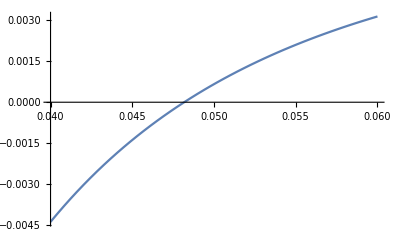

```mathematica
Plot[7000*10^-6-(((9810m)/(γ*25π*(1+2*1.25^2))+2)/(√(((9810m)/(γ*25π*(1+2*1.25^2))+2)^2+25))-((9810m)/(γ*25π*(1+2*1.25^2)))/(√(((9810m)/(γ*25π*(1+2*1.25^2)))^2+25))),{m,0.04,0.06}]
```

```mathematica
Assuming[m>0,Solve[(((9810m)/(γ*25π*(1+2*1.25^2))+2)/(√(((9810m)/(γ*25π*(1+2*1.25^2))+2)^2+25))-((9810m)/(γ*25π*(1+2*1.25^2)))/(√(((9810m)/(γ*25π*(1+2*1.25^2)))^2+25)))==7000*10^-6,m]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{m→0.048175}}